```mathematica
(*Here to search for the feasible region the process is divided into four filters to save computational time. First filter only uses five steps and then evaluate if any of the cases fall on the ground that is z<=0. Then remove these points and the filter continue to increase the number of steps until 250. This is deemed to be sufficient to investigate the influence of the input parameters and inditial condition on the feasible region. Later on for Figure 4, 6 and 8 after selecting the biologically relevant parameters and initial condition complete precedure is appplied where total number of steps are 1000 and desired convergence is also set.*)
```

## ytD0 0.03

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=5;(*number of steps*)

Subscript[zf, 1]=0;(*z foot position whihc is zero all the times*)
Subscript[yf, 1]=0;(*initial y foot position*)
Subscript[yDe, 1]=-0.05;(*initial y position of the center of mass*)
Subscript[zDe, 1]=1;(*initial z position of the center of mass*)
Subscript[yPDe, 1]=0.03;(*initial y speed*)
Subscript[zPDe, 1]=0;(*initila z speed*)

l00=1;(*l_0 *)

Subscript[tDe, 1]=0;(*starting time*)
period=(4Pi);(*this time window is fixed to search for the stepping condition*)

mtil=Table[ϕ,{ϕ,0.05,0.6,(0.6-0.05)/30}];(*phi points*)
gtil=Table[γ,{γ,0.0001,0.06,(0.06-0.0001)/30}];(*gamma points*)
(*combining these mtil and gtil we get the grid in the phi gamma plane*)
nE2=Length[mtil];
nE3=Length[gtil];
```

```mathematica
Quiet[Table[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}](*to be used in finding the stepping time*),
parameters=Table[{ldev->1.5*l00,l0->l00,b->0,ϕ->mtil[[p]],γ->gtil[[q]]},{p,1,nE2}](*ldev is ld and b is damping whihc is zero in model*),
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])](*equilinbrium length of spring*),
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2](*tripod length*),
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t])(*spring force*),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t])(*damping force whihc is zero (simplified)*),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}](*solving the system numerically*),

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]](*y trajectory*),
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]](*z trajectory*),
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t](*y velocity*),
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t](*z velocity*),

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
](*using FindRoot to list all the posiible stepping times*),

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&](*from the list of times selecting times that is greater than starting time*),
ys=Flatten[(Subscript[dsoly, k]/.t->times)](*finding the speed at all possible times*),
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}](*substracting the speeds at sptepping times from the initial speed, and getting true and false when the difference is les than 10^-6*),


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]](*picking the minimum time corresponding to true values from the list. This is the starting point of the next step*),



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1])(*y position at the stepping time*),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1])(*z position at the stepping time*),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1])(*y velocity at the steppin time*),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1])(*z velocity at the stepping time*),

Subscript[zf, k+1]=0(*z foot position always 0*),
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]](*next foot position*)

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]](*z position function for 5 steps *),
Subscript[condi, p,q]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&](*finding if z is greater than equal to 0 at the total time of the 5 steps*),
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-6(*checking the tjrehold in the z velocity*),
Abs[(Abs[Subscript[yPDe, nE+1]]-Abs[Subscript[yPDe, nE]])]<10^-6(*checking the threshold in y velocity, whihc is always fullfiled as stepping is based on it*),
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-6(*checking the threshold in z velocity*)}


},{p,1,nE2}],{q,1,nE3}]];
```

```mathematica
mg=Table[Table[{mtil[[i]],gtil[[j]]},{i,1,nE2}],{j,1,nE3}](*Grid points phi gamma *);
conditions=Table[Table[Subscript[condi, p,q],{p,1,nE2}],{q,1,nE3}](*saving conditions in normal variable than subscript one*);
conditions1=Table[If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions[[q]],{q,1,nE3}](*putting false wher the values are other than true or false*);
```

```mathematica
(*checking if the the system is falling or not*)
fistCon=Table[Table[First[conditions1[[q,p]]],{p,1,nE2}],{q,1,nE3}]
(*points that are not falling*);
truepoints=Table[Pick[mg[[q]],fistCon[[q]],True],{q,1,nE3}]
(*points that are falling*);
falsepoints=Flatten[Table[Pick[mg[[q]],fistCon[[q]],False],{q,1,nE3}],1];
```

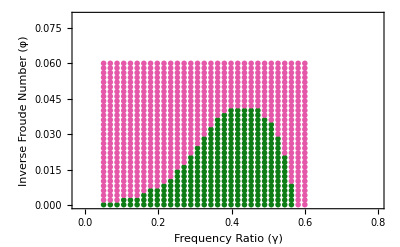

```mathematica
Show[ListPlot[{Style[Flatten[truepoints,1],ColorData["AvocadoColors",0.3]],Style[falsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}],

Plot[{p21},{m,0.23,2},PlotStyle->ColorData["Rainbow",0],PlotRange->{All,{0,2}}]
,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Second Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=20;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.03;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=Flatten[truepoints,1];
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions2=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
firstCon2=Table[First[conditions2[[p]]],{p,1,nE2}];
truepoints2=Pick[Flatten[truepoints,1],firstCon2,True];
falsepoints2=Pick[Flatten[truepoints,1],firstCon2,False];
```

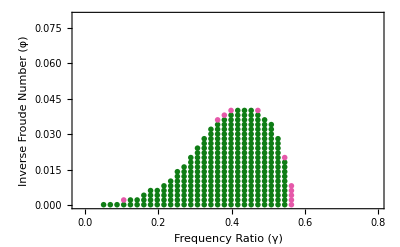

```mathematica
Show[ListPlot[{Style[truepoints2,ColorData["AvocadoColors",0.3]],Style[falsepoints2,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Third Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=50;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
l00=1;
Subscript[yPDe, 1]=0.03;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=truepoints2;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions3=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon3=Table[conditions3[[i,;;2]]=={True,True},{i,1,Length[conditions3]}];
truepoints4=Pick[truepoints2,secondCon3,True];
falsepoints4=Pick[truepoints2,secondCon3,False];
```

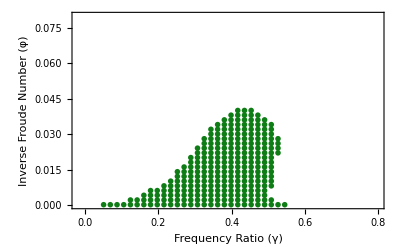

```mathematica
Show[ListPlot[{Style[truepoints4,ColorData["AvocadoColors",0.3]](*,Style[falsepoints4,ColorData["FruitPunchColors",0.9]]*)},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Fourth Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=300;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.03;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=falsepoints4;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions4=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon4=Table[conditions4[[i]]=={True,True,True},{i,1,Length[conditions4]}];
truepoints5=Pick[falsepoints4,secondCon4,True];
falsepoints5=Pick[falsepoints4,secondCon4,False];
```

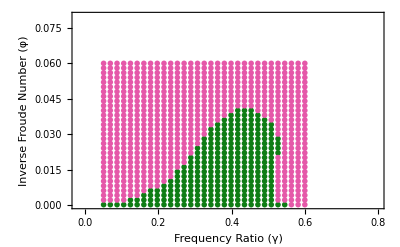

```mathematica
finaltruepoints=Union[truepoints5,truepoints4];
finalfalsepoints=Union[falsepoints5,falsepoints2,falsepoints];
Show[ListPlot[{Style[finaltruepoints,ColorData["AvocadoColors",0.3]],Style[finalfalsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofytD003TPU.mx",finaltruepoints];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofytD003FPU.mx",finalfalsepoints];
```

## ytD0 0.05

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=5;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
l00=1;
Subscript[yPDe, 1]=0.05;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

mtil=Table[ϕ,{ϕ,0.025,0.6,(0.6-0.025)/30}];
gtil=Table[γ,{γ,0.0001,0.06,(0.06-0.0001)/30}];
nE2=Length[mtil];
nE3=Length[gtil];
```

```mathematica
Quiet[Table[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*l00,l0->l00,b->0,ϕ->mtil[[p]],γ->gtil[[q]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p,q]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[yPDe, nE+1]]-Abs[Subscript[yPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-6}


},{p,1,nE2}],{q,1,nE3}]];
```

```mathematica
mg=Table[Table[{mtil[[i]],gtil[[j]]},{i,1,nE2}],{j,1,nE3}];
conditions=Table[Table[Subscript[condi, p,q],{p,1,nE2}],{q,1,nE3}];
conditions1=Table[If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions[[q]],{q,1,nE3}];
```

```mathematica
fistCon=Table[Table[First[conditions1[[q,p]]],{p,1,nE2}],{q,1,nE3}];
truepoints=Table[Pick[mg[[q]],fistCon[[q]],True],{q,1,nE3}];
falsepoints=Flatten[Table[Pick[mg[[q]],fistCon[[q]],False],{q,1,nE3}],1];
```

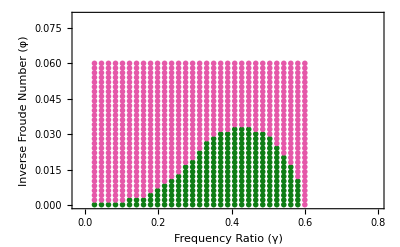

```mathematica
Show[ListPlot[{Style[Flatten[truepoints,1],ColorData["AvocadoColors",0.3]],Style[falsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]
,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Second Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=20;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.05;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=Flatten[truepoints,1];
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions2=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
firstCon2=Table[First[conditions2[[p]]],{p,1,nE2}];
truepoints2=Pick[Flatten[truepoints,1],firstCon2,True];
falsepoints2=Pick[Flatten[truepoints,1],firstCon2,False];
```

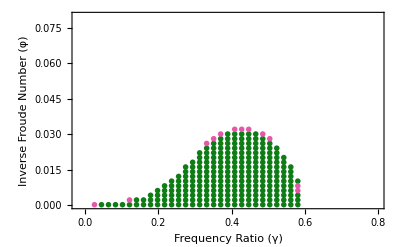

```mathematica
Show[ListPlot[{Style[truepoints2,ColorData["AvocadoColors",0.3]],Style[falsepoints2,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Third Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=40;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.05;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=truepoints2;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions3=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon3=Table[conditions3[[i,;;2]]=={True,True},{i,1,Length[conditions3]}];
truepoints4=Pick[truepoints2,secondCon3,True];
falsepoints4=Pick[truepoints2,secondCon3,False];
```

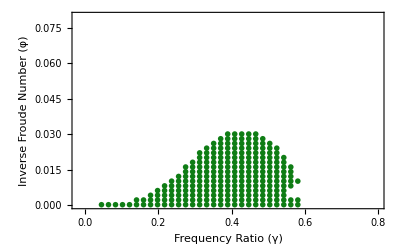

```mathematica
Show[ListPlot[{Style[truepoints4,ColorData["AvocadoColors",0.3]](*,Style[falsepoints4,ColorData["FruitPunchColors",0.9]]*)},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Fourth Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=250;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.05;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=falsepoints4;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions4=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon4=Table[conditions4[[i,;;2]]=={True,True},{i,1,Length[conditions4]}];
truepoints5=Pick[falsepoints4,secondCon4,True];
falsepoints5=Pick[falsepoints4,secondCon4,False];
```

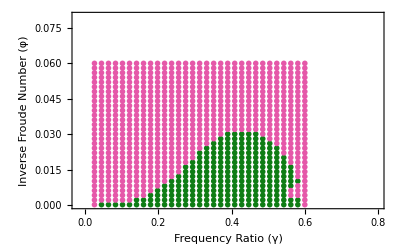

```mathematica
finaltruepoints=Union[truepoints5,truepoints4];
finalfalsepoints=Union[falsepoints5,falsepoints2,falsepoints];
Show[ListPlot[{Style[finaltruepoints,ColorData["AvocadoColors",0.3]],Style[finalfalsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofytD005TPU.mx",finaltruepoints];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofytD005FPU.mx",finalfalsepoints];
```

```mathematica
groupedHpoints=Values@GroupBy[SortBy[finaltruepoints,Last](*Sorting the points according to ascending order of second element*),#[[2]]&];
groupedVpoints=Values@GroupBy[SortBy[finaltruepoints,First](*Sorting the points according to ascending order of second element*),#[[1]]&];
listHbound=Flatten[Table[{First[groupedHpoints[[i]]],Last[groupedHpoints[[i]]]},{i,1,Length[groupedHpoints]}],1];
listVbound=Flatten[Table[{First[groupedVpoints[[i]]],Last[groupedVpoints[[i]]]},{i,1,Length[groupedVpoints]}],1];
boundarypoints=DeleteDuplicates[Join[listHbound,listVbound]];
```